## wobbling frequencies

```mathematica
j=5.5;
j1[θ_]:=j*Cos[θ*π/180];
j2[θ_]:=j*Sin[θ*π/180]
omega[i_,a1_,a2_,a3_,θ_]:=(((2i+1)(a2-a1-(a2*j2[θ])/i)-2*a1*j1[θ])*((2i+1)(a3-a1)-2a1*j1[θ])-(a3-a1)*(a2-a1-(a2*j2[θ])/i))^(1/2);
omegaPrime[i_,a1_,a2_,a3_,θ_]:=(((2i+1)(a2-a1-(a2*j2[θ])/i)+2*a1*j1[θ])*((2i+1)(a3-a1)+2a1*j1[θ])-(a3-a1)*(a2-a1-(a2*j2[θ])/i))^(1/2);
```

## Test wobbling frequencies with the C++ algorithm

### July 31 update

```mathematica
Print[omega[9.5,1/(2*30),1/(2*100),1/(2*80),30]," ; ",omega[9.5,1/(2*30),1/(2*100),1/(2*80),30+180]]
```

0.39298 ; 0.0464145

```mathematica
Print[omegaPrime[9.5,1/(2*30),1/(2*100),1/(2*80),30]," ; ",omegaPrime[9.5,1/(2*30),1/(2*100),1/(2*80),30+180]]
```

0.0706649 ; 0.36498

```mathematica
(*I1=129 I2=3 I3=52 theta=-160
E_RMS=0.21061*)
```

```mathematica
a1=1/(2*129);
a2=1/(2*3);
a3=1/(2*52);
θ=-160;
```

```mathematica
p1=ListPlot[Table[{x,omega[x,a1,a2,a3,θ]},{x,7.5,25.5,2}],AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Red,Thick},FrameLabel->{"I [ℏ]","δ ω_I(θ;θ-π) [MeV]"},LabelStyle->{Black,Bold,18, FontFamily->"Times New Roman"},Epilog->Inset[Framed[Style["θ=-160^o",Black,Bold,18, FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{0.75,0.25}]]];
```

```mathematica
p2=ListPlot[Table[{x,omega[x,a1,a2,a3,θ]},{x,8.5,16.5,2}],AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Black,Thick},FrameLabel->{"I [ℏ]","δ ω_I(θ;θ-π) [MeV]"},LabelStyle->{Black,Bold,18, FontFamily->"Times New Roman"},Epilog->Inset[Framed[Style["θ=-160^o",Black,Bold,18, FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{0.75,0.25}]]];
```

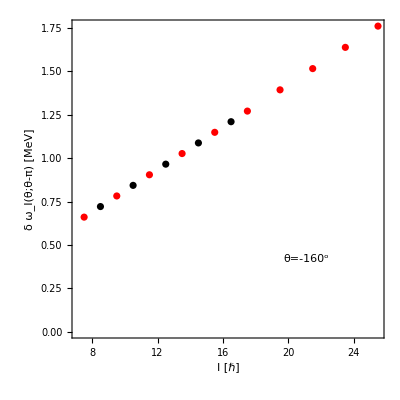

```mathematica
Show[p1,p2]
```

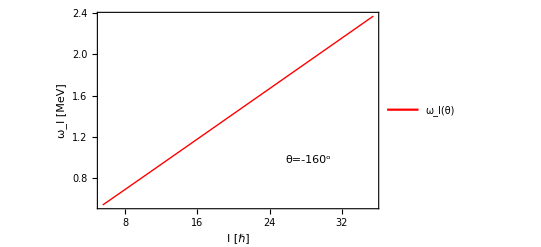

```mathematica
Plot[{omega[x,a1,a2,a3,θ]},{x,5.5,35.5},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Red,Thick},FrameLabel->{"I [ℏ]","ω_I [MeV]"},LabelStyle->{Black,Bold,20, FontFamily->"Times New Roman"},PlotLegends->Placed[{"ω_I(θ)"},{0.25,0.75}],Epilog->Inset[Framed[Style["θ=-160^o",Black,Bold,20, FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{0.75,0.25}]]]
```

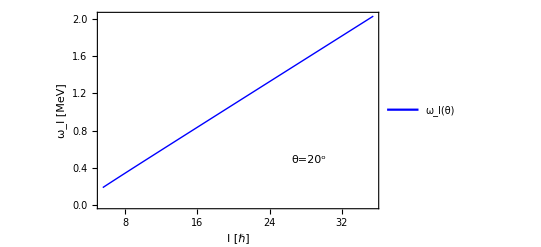

```mathematica
Plot[{omega[x,a1,a2,a3,20]},{x,5.5,35.5},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Blue,Thick},FrameLabel->{"I [ℏ]","ω_I [MeV]"},LabelStyle->{Black,Bold,20, FontFamily->"Times New Roman"},PlotLegends->Placed[{"ω_I(θ)"},{0.25,0.75}],Epilog->Inset[Framed[Style["θ=20^o",Black,Bold,20, FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{0.75,0.25}]]]
```

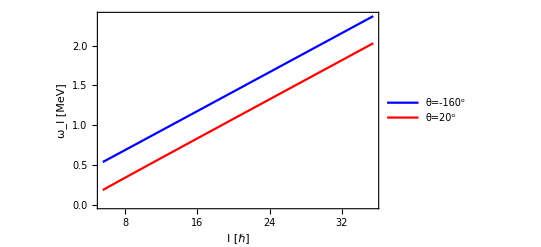

```mathematica
Plot[{omega[x,a1,a2,a3,-160],omega[x,a1,a2,a3,20]},{x,5.5,35.5},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{{Blue},{Red}},FrameLabel->{"I [ℏ]","ω_I [MeV]"},LabelStyle->{Black,Bold,20, FontFamily->"Times New Roman"},PlotLegends->Placed[{"θ=-160^o","θ=20^o"},{0.25,0.75}](*Epilog->Inset[Framed[Style["θ=-160^o",Black,Bold,20, FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{0.75,0.25}]]*)]
```